```mathematica
f1[x_] := 1/(1+x^2)
xObs := Range[-2, 2, 0.3]
fObs := f1[xObs]
```

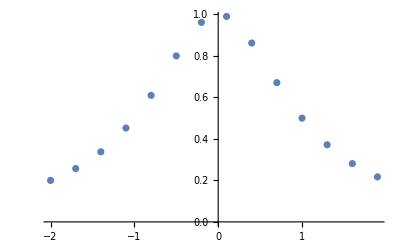

```mathematica
ListPlot[Transpose @ {xObs, fObs}]
```

```mathematica
lagrange[x0_, xVals0_, fVals0_] := Module[{x =x0, xVals = xVals0, fVals=fVals0, nObs=Length[xVals0]},
allValues = Table[If[i==k, 1, (x-xVals[[i]])/(xVals[[k]]-xVals[[i]])],{i, 1, nObs}, {k, 1, nObs}];
LkVals = Times @@ allValues;
Pn = LkVals . fVals;
Pn
]
```

```mathematica
zObs := Table[Subscript[z, i],{i, 1, 3}]
fObs := Table[Subscript[f, i],{i, 1, 3}]
l1[x_]:=lagrange[x, zObs, fObs]
```

```mathematica
Simplify[InterpolatingPolynomial[Transpose[{zObs, fObs}], x]]
```

f_1+(x-z_1) ((f_1-f_2)/(z_1-z_2)+((x-z_2) ((-f_1+f_2)/(z_1-z_2)+(f_2-f_3)/(z_2-z_3)))/(-z_1+z_3))

```mathematica
Manipulate[
domain = Subdivide[-5., 5, n-1];
range = f1[domain];
l2[x_] = lagrange[x, domain, range];
p1 = Plot[{l2[x], f1[x]}, {x, -5.,5.}, PlotLabel->"n=" +  n, PlotRange->{-0.2, 1}];
p2 =ListPlot[Transpose @ {domain, range}, PlotStyle->{PointSize[0.02]}];
g1 = Show[p1, p2];
g2 = Plot[Abs[l2[x] /f1[x] - 1], {x, -5., 5.}, PlotRange->{0, 1}];
GraphicsRow[{g1, g2}],
{n, 2, 30, 2}]
```